# HW Sept 2nd

Here is the first set of parameters.

-Graphics3D-

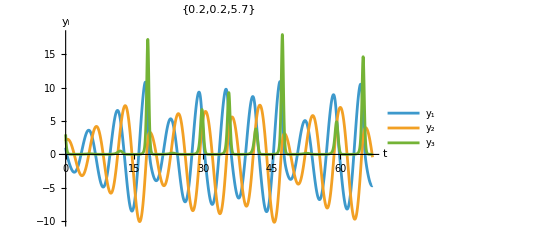

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z,  x + a y, b +z (x-c)}
y0={1,2,3}; TMax=67;
{a,b,c}={0.2,0.2,5.7};
ySol=NDSolveValue[
{y'[t]==f[{a,b,c}][y[t]],y[0]==y0},
y,{t,0, TMax}];
ParametricPlot3D[ySol[t],{t,0,TMax},PlotRange->All,
AxesLabel->{"x","y","z"},
PlotLabel->{a,b,c}]
Plot[{ySol[t]⟦1⟧,ySol[t]⟦2⟧,ySol[t]⟦3⟧},{t,0, TMax},
AxesLabel->{"t","y_i"},
PlotLegends->{"y_1","y_2","y_3"},
PlotLabel->{a,b,c}]
```